# Estimating Pi

## ACM40960 Project

## 1. Archimedes’ Method

### 1.1. Illustrating the Approximation Method using a Manipulate Function

```mathematica
(* Create a Manipulate function for a range of values of n, where n is the number of sides of the polygon. Locally define the variables 'bigpoly', 'smallpoly', 'bigestimate', and 'smallstimate' using the Module function. *)
Manipulate[Module[{bigpoly, smallpoly, bigestimate, smallestimate},

(* Define the variable 'bigpoly' to be a polygon with n sides and a radius of 1/(Cos[180]/n) degrees. *)
bigpoly = RegularPolygon[1/Cos[180/n Degree],n];

(* Define the variable 'smallpoly' to be a polygon with n points on the unit circle. *)
smallpoly=Polygon[CirclePoints[1,n]];

(* Define the two estimates of Pi using Tan and Sin. *)
bigestimate = n Tan[180/n Degree];
smallestimate = n Sin[180/n Degree];

(* Display both of the polygons along with the unit circle, using differing colours and outlines. *)
Show[{Graphics[{Opacity[0.15],EdgeForm[Directive[Thick, Dashed, Blue]],Blue, Rotate[smallpoly, 90 Degree]}], 

			    Graphics[{Opacity[0.15],EdgeForm[Directive[Thick, Dashed, Red]],Red, bigpoly, Opacity[0.15]}]},

			      Graphics[Circle[{0,0}]], ImageSize->Medium, Axes->True,

			     (* Print the two estimates at the top of the plot.*)
			      PlotLabel->{N[smallestimate],N[bigestimate]},LabelStyle->Directive[Bold,Black]]],
(* Specify the values of n to be used. *)
{{n,6,"n"}, {6,12,24,48,96},RadioButton}]
```

### 1.2. Approximation Results and Convergence

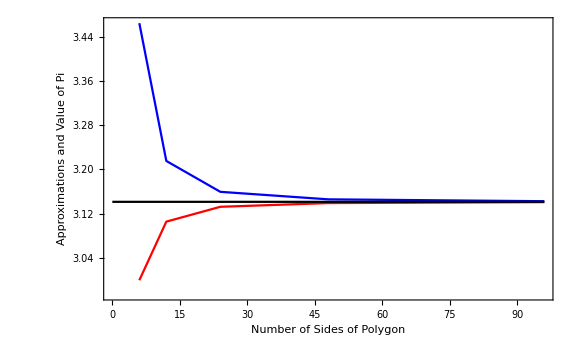

```mathematica
GraphicsRow[

(* Create two tables of two dimensional coordinates, where the x coordinate is n, and the y coordinate is the numerical value of the perimeter of the circumscribed and inscribed polygons.*)
{Show[ListLinePlot[{
Table[{n,N[n Sin[180/n Degree]]},{n,{6,12,24,48,96}}],
Table[{n,N[n Tan[180/n Degree]]},{n,{6,12,24,48,96}}]},

(* Specify desired colours and plot a horizontal line for the true value of Pi. *)
PlotStyle->{Red,Blue}],Plot[π,{x,0,96},PlotStyle->Black], 

       (* Include a frame and specify the and axes labels, as well as the size of the plot. *)
Frame->True,FrameLabel->{"Number of Sides of Polygon \n ","  \n Approximations and Value of Pi"},RotateLabel->True,ImageSize->Large,LabelStyle->Directive[Bold,Black]],

	(* Add a legend to the plot. *)
LineLegend[{Blue,Black,Red},{"Circumscribed Polygon","Inscribed Polygon","Pi"}]}]
```

## 2. Quadrant Method

### 2.1. Illustrate Areas

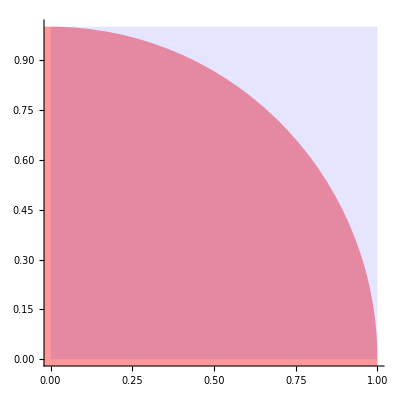

```mathematica
(* Plot a unit square and a quadrant of the unit circle. Use different colours to distinguish the areas. Show the x and y axes. *)
Show[Graphics[{Opacity[0.4],Red,Disk[{0,0},1]}],Graphics[{Opacity[0.1],Blue,Rectangle[]}],PlotRange->{{0,1},{0,1}},Axes->True]
```

### 2.2. Demonstrate the Method Using a Manipulate Function

```mathematica
Manipulate[
(* Use the RandomPoint[] function to generate a list of n pseudorandom points uniformly distributed in the region Rectangle[]. Rectangle[] is equivalent to a unit square. *)
points = RandomPoint[Rectangle[],n];

(* RegionMember[] gives True if the point is a member of the region Disk[{0,0},1], which is a disk of radius 1 with centre at {0,0}. *)
inside = RegionMember[Disk[{0,0},1]];

(* Pick out the elements from the list of points for which inside[points] is True, i.e. which points are inside of the disk. Colour these selected points red. *)
Show[Graphics[{Point[points],Red,Point[Pick[points,inside[points]]],AbsolutePointSize[3]}],Graphics[Circle[{0,0}], Axes->True],

(* Show the unit square in blue. *)
Graphics[{Opacity[0.1],Blue,Rectangle[]}],PlotRange->{{0,1},{0,1}},

(* Print the approximated value of Pi as the title of the plot. *)
PlotLabel->N[(Length[Pick[points,inside[points]]]/Length[points])4,4],LabelStyle->Directive[Bold,Black],Axes->True],

(* Specify the values of n to be used. *)
{{n,10^2,"n"},{10^2,10^3,10^4,10^5},RadioButton}]
```

### 2.3. Three Trials for Different Seeds

ESTIMATED RUN TIME: APPROXIMATELY 20 MINUTES

```mathematica
list1 = List[];SeedRandom[100]; (* Create an empty list and specify a random seed to be used. *)

table1=Table[ (* Store the estimates in a table. *)

(* Generate two pseudo random numbers in the range [0,1]. *)
x=RandomReal[];y=RandomReal[]; 

(* If the generated coordinate is inside of the quadrant, add 1 to the list. If it is outside of the quadrant, add 0 to the list. *)
If[x^2+y^2<=1,list1=Append[list1,1],list1=Append[list1,0]]; 

(* The formula for an estimate of Pi is the proportion of points that are inside the quadrant, multiplied by 4. *)
4 Total[list1]/Length[list1],

(* Repeat this up until 10^5. *)
{n,1,10^5}];

(* Repeat this method for a different random seed. *)
list2 = List[];SeedRandom[200];
table2=Table[x=RandomReal[];y=RandomReal[];
If[x^2+y^2<=1,list2=Append[list2,1],list2=Append[list2,0]];
4 Total[list2]/Length[list2],{n,1,10^5}];

(* Repeat this method for another different random seed. *)
list3 = List[];SeedRandom[300];
table3=Table[x=RandomReal[];y=RandomReal[];
If[x^2+y^2<=1,list3=Append[list3,1],list3=Append[list3,0]];
4 Total[list3]/Length[list3],{n,1,10^5}];

(* Compute the average of the three tables of estimates. *)
average3 = (table1+table2+table3)/3;
```

## 3. Gamma Function Integral Method

### 3.1. Function to Demonstrate Method

This function can be used to obtain an estimate of π using the gamma function integral for any number of trials. This is computationally much faster than the next section, as it only calculates the π estimate at a specific n, rather than a list of estimates for 1 up to n.

```mathematica
gamma[n_]:={Quiet[(* Mute messages. *)

estimates1=List[];SeedRandom[100]; (* Create an empty list and set a random seed. *)
For[i=1,i<n+1,i++, (* Create a For loop from 1 to n. *)
u=RandomReal[]; (* Compute a random number in the range [0,1]. *)
integral=E^(1-1/u)/(u^2 √(1/u-1)); (* Compute the expression. *)
estimates1=Append[estimates1,integral]];(* Add this evaluated expression to the list. *)
approx1 = Mean[estimates1]^2 ;(* Compute the mean of the estimates and square it. *)


estimates2=List[];SeedRandom[200]; (* Repeat for a new seed. *)
For[i=1,i<n+1,i++, 
u=RandomReal[];
integral=E^(1-1/u)/(u^2 √(1/u-1)); 
estimates2=Append[estimates2,integral]];
approx2 = Mean[estimates2]^2;


estimates3=List[];SeedRandom[300]; (* Repeat for a new seed. *)
For[i=1,i<n+1,i++, 
u=RandomReal[];
integral=E^(1-1/u)/(u^2 √(1/u-1)); 
estimates3=Append[estimates3,integral]];
approx3 = Mean[estimates3]^2;

(* Compute the mean of the three lists of estimates. *)
mean=(approx1 +approx2+approx3)/3]}
```

Estimate π for 10^2, 10^3, 10^4, and 10^5.

```mathematica
gammaestimates=Table[{n,gamma[n]},{n,{10^2,10^3,10^4,10^5}}]
```

{{100,{3.34248}},{1000,{3.17582}},{10000,{3.0081}},{100000,{3.14692}}}

### 3.2. Three Trials for Different Seeds

ESTIMATED RUN TIME: APPROXIMATELY 5 MINUTES

```mathematica
Quiet[(* Mute error messages. *)

estimates=List[];SeedRandom[100]; (* Create an empty list and set a random seed. *)
tab1=Table[u=RandomReal[]; (* Create a table of the squared mean from 1 to n of the expression evaluated for a random value of u in the range [0,1]. *)
integral=E^(1-1/u)/(u^2 √(1/u-1)); 
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];

	(* Repeat for two more different random seeds. *)
estimates=List[];SeedRandom[200];
tab2=Table[u=RandomReal[];integral=E^(1-1/u)/(u^2 √(1/u-1));
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];

estimates=List[];SeedRandom[300];
tab3=Table[u=RandomReal[];integral=E^(1-1/u)/(u^2 √(1/u-1));
estimates=Append[estimates,integral];Mean[estimates]^2,{n,1,10^5}];]

(* Compute the mean of all of the estimates. *)
average5=(tab1+tab2+tab3)/3;
```

## 4. Gregory-Leibniz Series Method

### 4.1. Function to Demonstrate Method

This function can be used to obtain an estimate of π using the Gregory-Leibniz series for any number of trials. This is computationally much faster than the next section, as it only calculates the π estimate at a specific n, rather than a list of estimates for 1 up to n.

```mathematica
gregory[n_]:={
(* Create an empty list. *)
list1=List[];
(* Choose a random seed. *)
SeedRandom[100];
(* Create a for loop. *)
For[i=1,i<n,i++,
(* Generate two pseudo random numbers in [0,1]. *)
x=RandomReal[];y=RandomReal[];
(* If y/x rounds to an even number, add 1 to the list. If it does not round to an even number, add 0 to the list. *)
If[EvenQ[Round[y/x]],list1=Append[list1,1],list1=Append[list1,0]]];
(* The estimate for π is 5 minus 4 times the proportion of random y/x's that rounded to an even number. *)
est1=N[5-4 Total[list1]/n];

(* Repeat for a different seed. *)
list2=List[];SeedRandom[200];
For[i=1,i<n,i++,x=RandomReal[];y=RandomReal[];If[EvenQ[Round[y/x]],list2=Append[list2,1],list2=Append[list2,0]]];est2=N[5-4 Total[list2]/n];

(* Repeat for another different seed. *)
list3=List[];SeedRandom[300];
For[i=1,i<n,i++,x=RandomReal[];y=RandomReal[];If[EvenQ[Round[y/x]],list3=Append[list3,1],list3=Append[list3,0]]];est3=N[5-4 Total[list3]/n];

(* Compute the mean of the three lists. *)
meanest=(est1+est2+est3)/3
}
```

Estimate π for 10^2, 10^3, 10^4, and 10^5.

```mathematica
gregoryestimates=Table[{n,gregory[n]},{n,{10^2,10^3,10^4,10^5}}]
```

{{100,{3.12}},{1000,{3.172}},{10000,{3.14733}},{100000,{3.14189}}}

### 4.2. Three Trials for Different Seeds

ESTIMATED RUN TIME: APPROXIMATELY 28 MINUTES

```mathematica
Quiet[
list1 = List[];SeedRandom[100];
gregtable1=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list1=Append[list1,1],list1=Append[list1,0]];
5-4 Total[list1]/Length[list1],{n,1,10^5}];
list2 = List[];SeedRandom[200];
gregtable2=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list2=Append[list2,1],list2=Append[list2,0]];
5-4 Total[list2]/Length[list2],{n,1,10^5}];
list3 = List[];SeedRandom[300];
gregtable3=Table[x=RandomReal[];y=RandomReal[];
If[EvenQ[Round[y/x]],list3=Append[list3,1],list3=Append[list3,0]];
5-4 Total[list3]/Length[list3],{n,1,10^5}];
average7=(gregtable1+gregtable2+gregtable3)/3;]
```

## 5. Error Bar Plots

### 5.1. Calculating the Mean Estimate and Standard Deviation

```mathematica
(* Get the mean estimates for each value of n. *)
means={{10^2,average5[[10^2]]},{10^3,average5[[10^3]]},{10^4,average5[[10^4]]},{10^5,Last[average5]}};
(* Compute the sample standard deviation for each value of n. *)
sd1={StandardDeviation[N[average5[[1;;10^2]]]],StandardDeviation[N[average5[[1;;10^3]]]], StandardDeviation[N[average5[[1;;10^4]]]], StandardDeviation[N[average5]]};
(* Multiply the sample standard deviation by 2. *)
sd2=Times[sd1,2];
(* Add and subtract one standard deviation from each of the mean estimates. *)
errors1={{10^2,average5[[10^2]]+sd1[[1]]},{10^3,average5[[10^3]]+sd1[[2]]},{10^4,average5[[10^4]]+sd1[[3]]},{10^5,Last[average5]+sd1[[4]]},
{10^2,average5[[10^2]]-sd1[[1]]},{10^3,average5[[10^3]]-sd1[[2]]},{10^4,average5[[10^4]]-sd1[[3]]},{10^5,Last[average5]-sd1[[4]]}};
(* Add and subtract two standard deviations from each of the mean estimates. *)
errors2={{10^2,average5[[10^2]]+sd2[[1]]},{10^3,average5[[10^3]]+sd2[[2]]},{10^4,average5[[10^4]]+sd2[[3]]},{10^5,Last[average5]+sd2[[4]]},
{10^2,average5[[10^2]]-sd2[[1]]},{10^3,average5[[10^3]]-sd2[[2]]},{10^4,average5[[10^4]]-sd2[[3]]},{10^5,Last[average5]-sd2[[4]]}};
```

### 5.2. Plotting the Mean Estimate and Error Bars

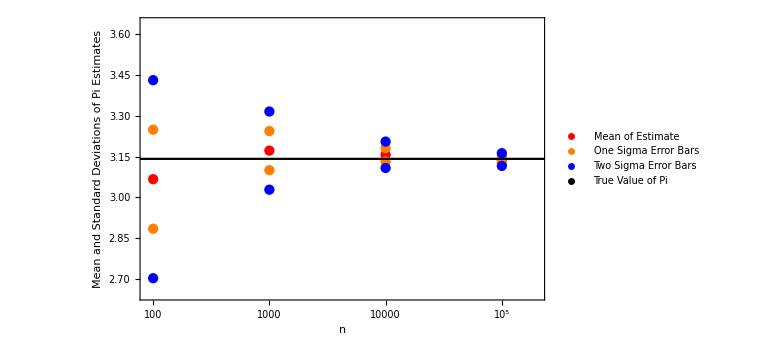

```mathematica
Show[
(* Plot the mean estimates together with the one and two sigma errors. *)
ListPlot[{means,errors1, errors2},
(* Apply a log scale to the x-axis. *)
ScalingFunctions->{"Log"}, 
ImageSize->Large, 
(* Choose the plot range so that π is centered. *)
PlotRange->{{90,200000},{π-0.5,π+0.5}}, 
(* Choose the colours of the points. *)
PlotStyle->{Red, Orange, Blue},
Frame->True,FrameLabel->{"n","  \n Mean and Standard Deviations of Pi Estimates"},
RotateLabel->True,LabelStyle->Directive[Black,Bold],
(* Add a legend to the plot. *)PlotLegends->Placed[PointLegend[{Red,Orange,Blue, Black},{"Mean of Estimate","One Sigma Error Bars","Two Sigma Error Bars", "True Value of Pi"}],{0.84,0.84}]],
(* Add the true value of π as a horizontal line. *)
Plot[π,{x,0,10^5},PlotStyle->Black]]
```

## 6. Relative Difference Plots

### 6.1. Calculating the Relative Difference

```mathematica
(* Compute the relative differences of the mean estimates to π. *)
relativediff=MapAt[Abs[#-π]/Max[Abs[#],Abs[π]]&,average5,All];
```

### 6.2. Plotting the Relative Difference Using Various Scaling

#### 6.2.1. Linear Plot

```mathematica
(* Plot the relative differences of the mean estimates to π on a linear scale. *)
```

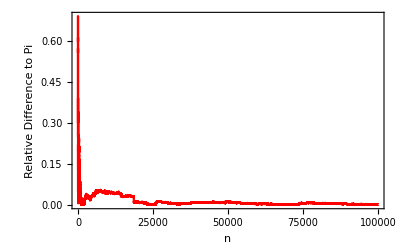

```mathematica
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

#### 6.2.2. Semi-Log Plot

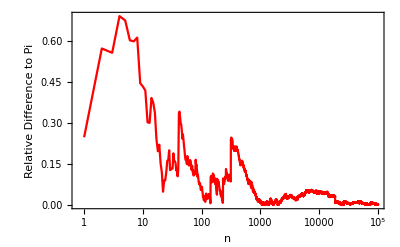

```mathematica
(* Plot the relative differences of the mean estimates to π using a log scale on the x axis. *)
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log"},
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

#### 6.2.3. Log-Log Plot

```mathematica
(* Plot the relative differences of the mean estimates to π using a log scale on the x axis and log scale on the y axis. *)
```

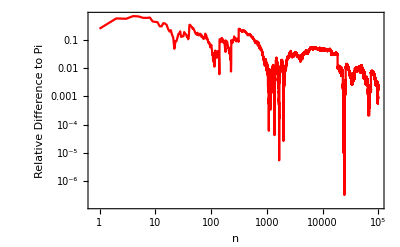

```mathematica
ListLinePlot[relativediff,PlotRange->Full ,PlotStyle->Red,
ScalingFunctions->{"Log","Log"},
Frame->True,FrameLabel->{"n","  \n Relative Difference to Pi"},
RotateLabel->True, LabelStyle->Directive[Black,Bold]]
```

## 7. Convergence Plots

```mathematica
Show[

(* Create a plot of the three tables of estimation values for different seeds. *)
ListLinePlot[{tab1, tab2, tab3},
(* Colour these values green. *)
PlotStyle->Green,
(* Add a legend to the plot and place in the top right corner. *)PlotLegends->Placed[PointLegend[{Green,Red,Black},{"Trials 1 - 3","Mean of the Trials","Pi"},LabelStyle->Bold],{0.84,0.86}]],
(* Plot the average of the values from the three tables. Colour this line red. *)
ListLinePlot[average5,PlotStyle->Red],
(* Include the true value of Pi as a black horizontal line. Assign labels to the axes. *)
Plot[π,{x,0,10^5},PlotStyle->Black],
ImageSize->Large,Frame->True,
FrameLabel->{"n","  \n Approximations and Value of Pi"},RotateLabel->True,
ImageSize->Large,LabelStyle->Directive[Black,Bold],
(* Choose the plot range so that the true value of Pi is centered. *)
PlotRange->{{0,100000},{π-0.2,π+0.2}}]
```

-Graphics-